## Setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot,LogLinearPlot,Histogram,DensityHistogram,ListStepPlot},Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

```mathematica
myLog[x_]:={x[[1]],x[[2]],Log[x[[3]]]}
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/xelatex","Ghostscript"->"/usr/bin/gs"];
myMaTeX[x_]:= MaTeX[x,"Preamble"->{"\\usepackage{fontspec}","\\setmainfont{DejaVu Serif}"},FontSize->16]
```

```mathematica
myMaTeX2[x_]:= MaTeX[x,FontSize->18]
```

## Load params & Test

```mathematica
particle="JPsi";
centrality="0-20";
```

```mathematica
myParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../input/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&];
myDict=Association[Table[If[StringContainsQ[myParams[[i,2]],","],myParams[[i,1]]->ToExpression/@StringSplit[myParams[[i,2]],","],myParams[[i,1]]->ToExpression[myParams[[i,2]]]],{i,1,Length[myParams]}]]
```

<|A→208,collisionType→0,particleType→0,alphas→0,lambdaQCD→0.308,qhat0→0.075,useCentrality→1,centralityEdges→{0,20,40,60,100},lp→1.5,massp→0.938,rootsnn→5023,Ny→21,Npt→81,y_min→-5.,y_max→5.,ptmin→0.1,ptmax→40.1|>

```mathematica
(* load variables from params file to automate some things below *)
roots = myDict["rootsnn"]
```

5023

```mathematica
roots=5023;
```

```mathematica
M =If[ myDict["particleType"]==0,9.45,3.43](*0 for JPsi and 1 for Upsilon*)
```

9.45

```mathematica
cE = Which[roots==5023,"5.02",roots==8160,"8.16"]
```

5.02

```mathematica
centEdges=myDict["centralityEdges"]
centBins=Transpose[{Drop[centEdges,-1],Drop[centEdges,1]}]
centTags=centBins/. {a_,b_}:>ToString@Row[{a,"-",b}]
```

{0,20,40,60,100}

{{0,20},{20,40},{40,60},{60,100}}

{0-20,20-40,40-60,60-100}

### General functions

```mathematica
Mperp2[pt_] = pt^2+M^2; (* GeV ^2 *)
Mperp[pt_] = Sqrt[Mperp2[pt]]; (* GeV *)
ymaxFunction[pt_] = Log[roots/Mperp[pt]];
ptmaxFunction[y_]=Sqrt[(roots Exp[-y])^2 - M^2];
```

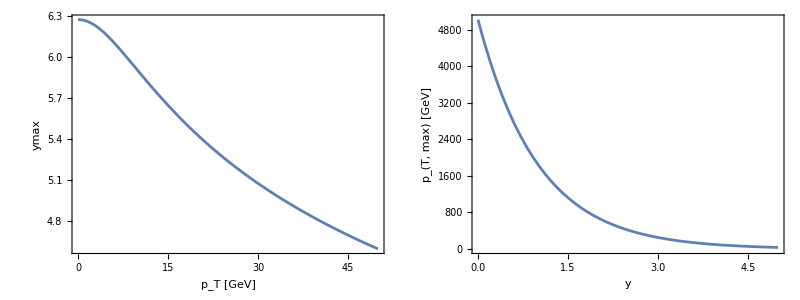

```mathematica
Grid[{{Plot[ymaxFunction[pt],{pt,0,50},FrameLabel->{"p_T [GeV]","ymax"}],Plot[ptmaxFunction[y],{y,0,5},FrameLabel->{"y","p_(T, max) [GeV]"}]}}]
```

## Read & Plot Data

### Read pA data

```mathematica
pAresultLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pAerrorLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAresultLog[[1,1]]
{ptmin,ptmax} = pAresultLog[[1,2]]
pAresult[y_,pt_]:=Exp[pAresultLog[y,pt]]
pAerror[y_,pt_]:=Exp[pAerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[pAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[pAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read AB data

```mathematica
ABresultLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_AB-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
ABerrorLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_AB-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = ABresultLog[[1,1]]
{ptmin,ptmax} = ABresultLog[[1,2]]
ABresult[y_,pt_]:=Exp[ABresultLog[y,pt]]
ABerror[y_,pt_]:=Exp[ABerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[ABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[ABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read pp data

```mathematica
ppresultLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pp-cross-section.tsv"],InterpolationOrder->Automatic];
ppresult[y_,pt_]:=Exp[ppresultLog[y,pt]]
```

```mathematica
Plot3D[ppresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read RAB data

```mathematica
RABresult=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RAB.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RABerror=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RAB.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} = RABresult[[1,1]];
{ptmin,ptmax} =RABresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RABresultU[y_,pt_]=RABresult[y,pt]+RABerror[y,pt];
RABresultL[y_,pt_]=RABresult[y,pt]-RABerror[y,pt];
```

```mathematica
myPlotY[pt_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_AB"},ImageSize->400,PlotRange->Automatic]
myPlotPT[y_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_AB"},ImageSize->400,PlotRange->Automatic]
```

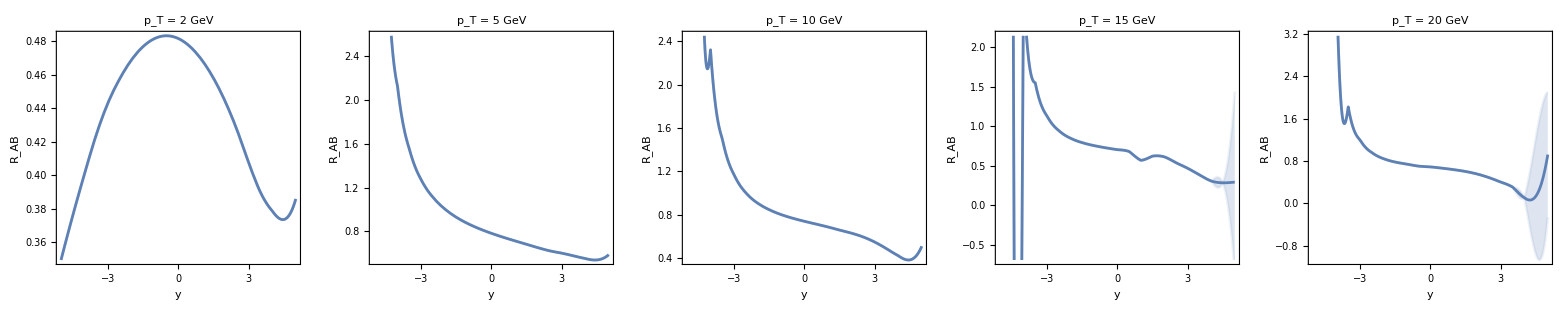

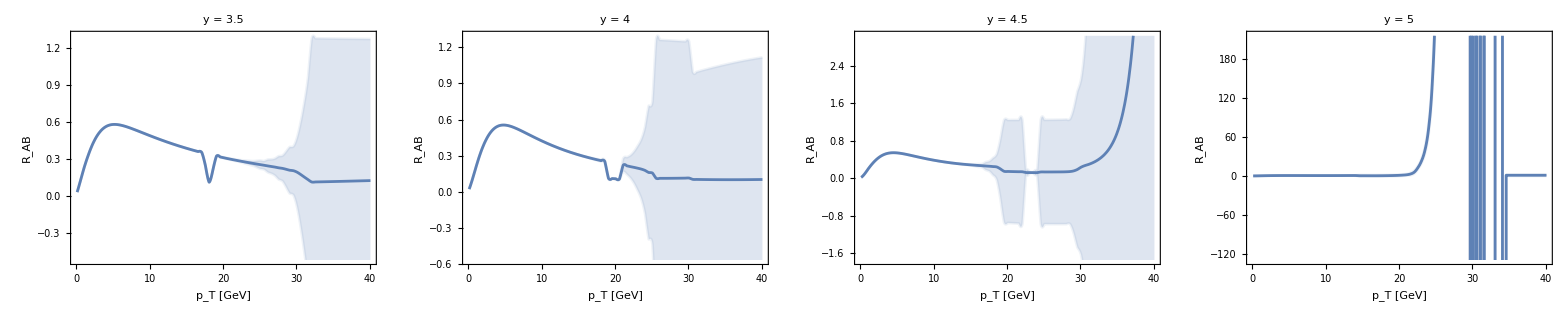

```mathematica
Grid[{{myPlotY[2],myPlotY[5],myPlotY[10],myPlotY[15],myPlotY[20]}}]
Grid[{{myPlotPT[3.5],myPlotPT[4],myPlotPT[4.5],myPlotPT[5]}}]
```

### Read RpA data

```mathematica
RpAresult=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAerror=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAresult[[1,1]];
{ptmin,ptmax} =RpAresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
mainPlot=Plot3D[RpAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Automatic,PlotRange->{0,1.5}];
(*Plot the plane at z=1*)
planePlot=Plot3D[1,{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Opacity[0.5,Red],Mesh->None];
Show[mainPlot,planePlot]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAresultU[y_,pt_]=RpAresult[y,pt]+RpAerror[y,pt];
RpAresultL[y_,pt_]=RpAresult[y,pt]-RpAerror[y,pt];
```

```mathematica
mypAPlotY[pt_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
mypAPlotPT[y_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
```

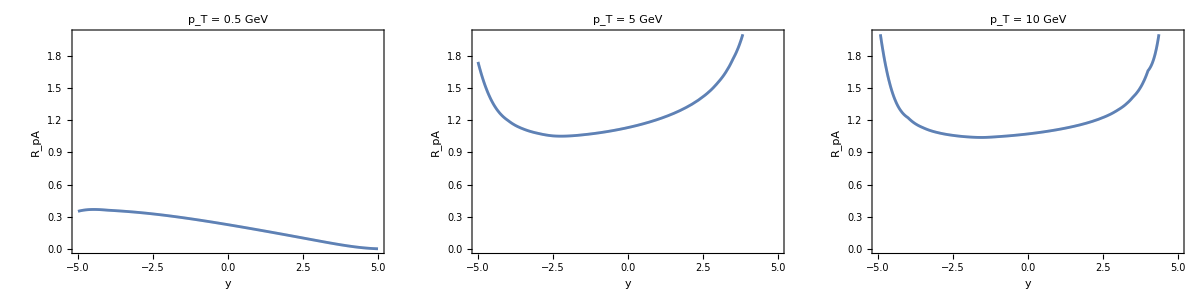

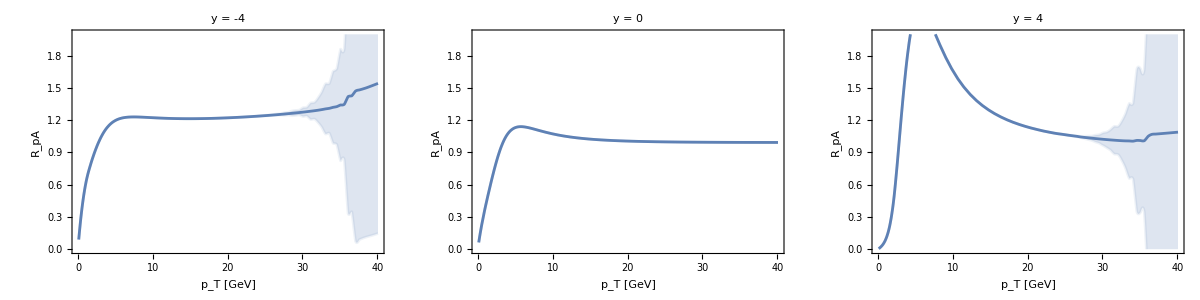

```mathematica
Grid[{{mypAPlotY[0.5],mypAPlotY[5],mypAPlotY[10]}}]
Grid[{{mypAPlotPT[-4],mypAPlotPT[0],mypAPlotPT[4]}}]
```

## RAB vs y & pT binned Plots

### Rapidity Dependent (p_T averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[RABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

{{-5.,0.0375526},{-4.5,0.0167791},{-4.,0.0125689},{-3.5,0.0106409},{-3.,0.00964422},{-2.5,0.00904282},{-2.,0.00862953},{-1.5,0.00831556},{-1.,0.00805287},{-0.5,0.00781391},{0.,0.00758256},{0.5,0.00734682},{1.,0.00709996},{1.5,0.00683385},{2.,0.00654951},{2.5,0.00626885},{3.,0.00600508},{3.5,0.00575953},{4.,0.00557427},{4.5,0.00568166}}

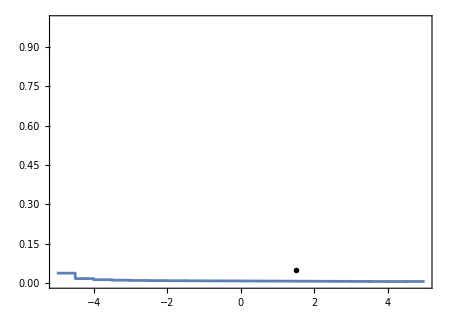

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.5,0.05}]}]
```

### p_T Dependent: Forward(1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

4

1.5

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

{0.360409,0.559056,0.613654,0.585331,0.545889,0.510356,0.444338,0.423534,0.419438,0.401107,0.376132,0.358342,0.328861,0.306278,0.282933,0.198039,-0.288403,-2.48764,-8.16266,-19.0843}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.360409},{2.5,0.559056},{5.,0.613654},{7.5,0.585331},{10.,0.545889},{12.5,0.510356},{15.,0.444338},{17.5,0.423534},{20.,0.419438},{22.5,0.401107},{25.,0.376132},{27.5,0.358342},{30.,0.328861},{32.5,0.306278},{35.,0.282933},{37.5,0.198039},{40.,-0.288403},{42.5,-2.48764},{45.,-8.16266},{47.5,-19.0843}}

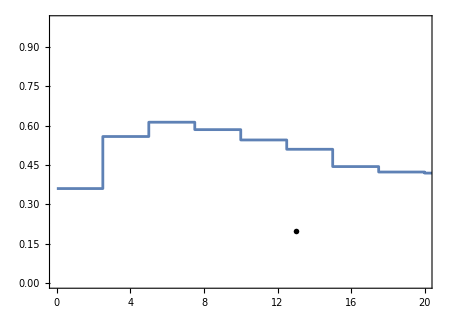

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Backward(2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

{0.380553,0.976007,1.51678,1.73292,2.22045,3.87235,6.76075,3.21344,6.00586,38.8134,3868.13,-9.96846×10^6,-1.84419×10^20,8.86527×10^30,31.5185,351.389,3474.64,12888.6,31120.6,60651.4}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.380553},{2.5,0.976007},{5.,1.51678},{7.5,1.73292},{10.,2.22045},{12.5,3.87235},{15.,6.76075},{17.5,3.21344},{20.,6.00586},{22.5,38.8134},{25.,3868.13},{27.5,-9.96846×10^6},{30.,-1.84419×10^20},{32.5,8.86527×10^30},{35.,31.5185},{37.5,351.389},{40.,3474.64},{42.5,12888.6},{45.,31120.6},{47.5,60651.4}}

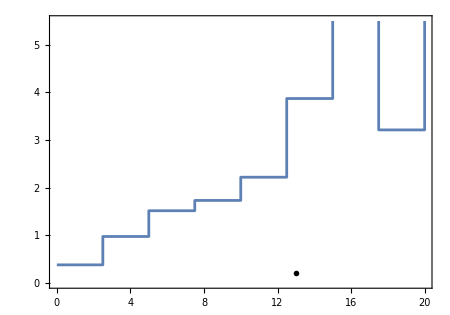

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0,5.5}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Mid(3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

{0.408474,0.69684,0.79835,0.768982,0.736653,0.70875,0.696042,0.693974,0.687345,0.679016,0.664258,0.627966,0.612005,0.61177,0.61168,0.611534,0.613537,0.629147,0.672508,0.757749}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.408474},{2.5,0.69684},{5.,0.79835},{7.5,0.768982},{10.,0.736653},{12.5,0.70875},{15.,0.696042},{17.5,0.693974},{20.,0.687345},{22.5,0.679016},{25.,0.664258},{27.5,0.627966},{30.,0.612005},{32.5,0.61177},{35.,0.61168},{37.5,0.611534},{40.,0.613537},{42.5,0.629147},{45.,0.672508},{47.5,0.757749}}

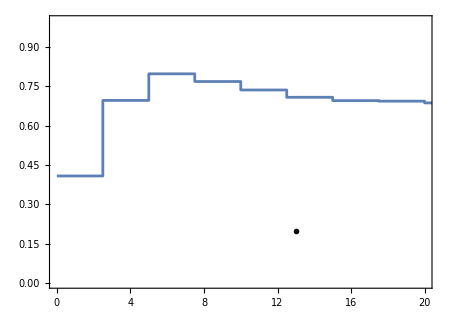

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.410108,0.710445,0.817939,0.785908,0.751553,0.721881,0.716945,0.709398,0.703863,0.696438,0.681902,0.643507,0.62784,0.629326,0.63098,0.632634,0.632663,0.612885,0.542452,0.390072}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.410108},{2.5,0.710445},{5.,0.817939},{7.5,0.785908},{10.,0.751553},{12.5,0.721881},{15.,0.716945},{17.5,0.709398},{20.,0.703863},{22.5,0.696438},{25.,0.681902},{27.5,0.643507},{30.,0.62784},{32.5,0.629326},{35.,0.63098},{37.5,0.632634},{40.,0.632663},{42.5,0.612885},{45.,0.542452},{47.5,0.390072}}

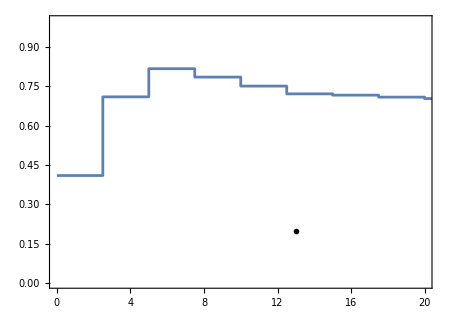

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

## RpA vs y & pT binned Plots

### Rapidity Dependent (p_T averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

{{-5.,1.20098},{-4.5,1.03136},{-4.,0.957602},{-3.5,0.917017},{-3.,0.89228},{-2.5,0.878232},{-2.,0.871546},{-1.5,0.868463},{-1.,0.867304},{-0.5,0.867613},{0.,0.86925},{0.5,0.872326},{1.,0.877283},{1.5,0.885149},{2.,0.898114},{2.5,0.921008},{3.,0.965027},{3.5,1.05756},{4.,1.27354},{4.5,2.02454}}

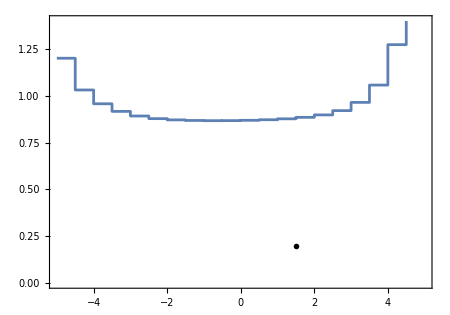

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.5,0.2}]}]
```

```mathematica
RpAresultPTavg[{-5,5}]
```

0.99981

### p_T Dependent: Forward(1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

4

1.5

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

{0.430348,1.17816,1.55081,1.39955,1.24603,1.15104,1.09308,1.0561,1.03126,1.01389,1.00104,0.989987,0.982214,0.976179,0.97448,0.971626,0.967119,0.957617,0.937664,0.901767}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.430348},{2.5,1.17816},{5.,1.55081},{7.5,1.39955},{10.,1.24603},{12.5,1.15104},{15.,1.09308},{17.5,1.0561},{20.,1.03126},{22.5,1.01389},{25.,1.00104},{27.5,0.989987},{30.,0.982214},{32.5,0.976179},{35.,0.97448},{37.5,0.971626},{40.,0.967119},{42.5,0.957617},{45.,0.937664},{47.5,0.901767}}

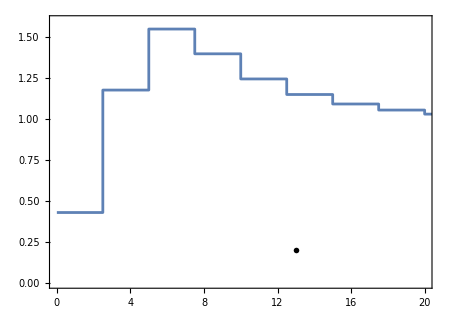

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0,1.6}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Backward(2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

{0.652517,1.04175,1.19328,1.17353,1.14639,1.13738,1.15373,1.23813,1.73392,7.26904,275.25,143000.,-1.00907×10^17,4.62857×10^27,2.34203,7.12511,38.4135,165.988,480.326,1072.18}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.652517},{2.5,1.04175},{5.,1.19328},{7.5,1.17353},{10.,1.14639},{12.5,1.13738},{15.,1.15373},{17.5,1.23813},{20.,1.73392},{22.5,7.26904},{25.,275.25},{27.5,143000.},{30.,-1.00907×10^17},{32.5,4.62857×10^27},{35.,2.34203},{37.5,7.12511},{40.,38.4135},{42.5,165.988},{45.,480.326},{47.5,1072.18}}

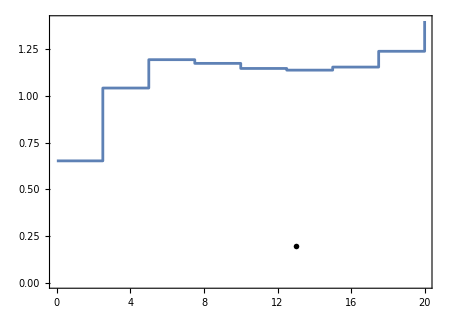

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Mid(3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

{0.596218,1.00698,1.15268,1.11258,1.06831,1.04061,1.02395,1.01365,1.00716,1.00293,1.00008,0.998134,0.996793,0.995878,0.995248,0.994815,0.994532,0.99444,0.994642,0.995238}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.596218},{2.5,1.00698},{5.,1.15268},{7.5,1.11258},{10.,1.06831},{12.5,1.04061},{15.,1.02395},{17.5,1.01365},{20.,1.00716},{22.5,1.00293},{25.,1.00008},{27.5,0.998134},{30.,0.996793},{32.5,0.995878},{35.,0.995248},{37.5,0.994815},{40.,0.994532},{42.5,0.99444},{45.,0.994642},{47.5,0.995238}}

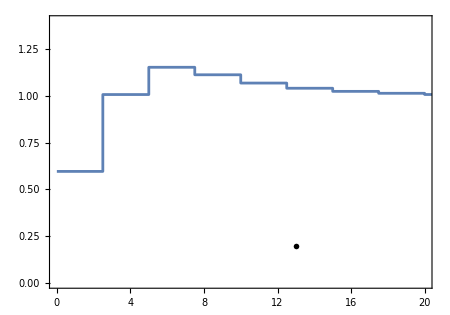

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.60872,0.999308,1.13388,1.09925,1.0603,1.03589,1.02123,1.01219,1.00654,1.00288,1.00044,0.998801,0.997689,0.996952,0.996463,0.996142,0.995955,0.996002,0.996466,0.997533}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.60872},{2.5,0.999308},{5.,1.13388},{7.5,1.09925},{10.,1.0603},{12.5,1.03589},{15.,1.02123},{17.5,1.01219},{20.,1.00654},{22.5,1.00288},{25.,1.00044},{27.5,0.998801},{30.,0.997689},{32.5,0.996952},{35.,0.996463},{37.5,0.996142},{40.,0.995955},{42.5,0.996002},{45.,0.996466},{47.5,0.997533}}

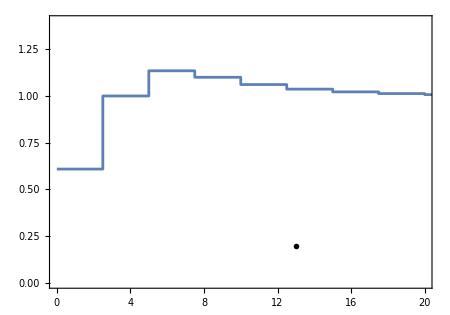

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```